```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/

```mathematica
(* Thickness *)
th=0.003;
```

## Setup and tests

### Hamiltonians

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
ha[4,tw,ts]//MatrixForm
```

(0 | 0 | 0 | -tw | 0 | ts | 0 | 0
0 | 0 | 0 | 0 | tw | 0 | ts | 0
0 | 0 | 0 | 0 | 0 | tw | 0 | ts
-tw | 0 | 0 | 0 | 0 | 0 | tw | 0
0 | tw | 0 | 0 | 0 | 0 | 0 | tw
ts | 0 | tw | 0 | 0 | 0 | 0 | 0
0 | ts | 0 | tw | 0 | 0 | 0 | 0
0 | 0 | ts | 0 | tw | 0 | 0 | 0)

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec,i=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hp[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

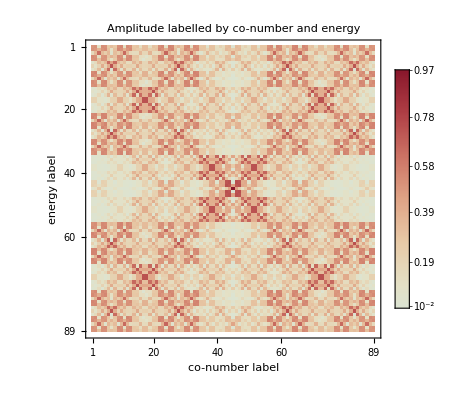

```mathematica
MatrixPlot [Abs[wf],FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

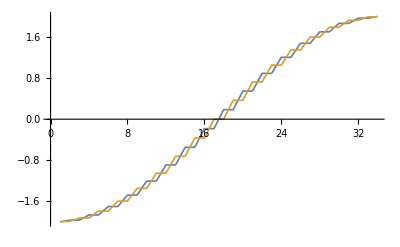

```mathematica
Block[{ts=1.,tw=1.,vpp,vpa,i=7},
vpp=Sort@Eigenvalues[hp[i,tw,ts]];
vpa=Sort@Eigenvalues[ha[i,tw,ts]];
ListPlot[{vpp,vpa},Joined->True,PlotStyle->Thickness[th]]
]
```

```mathematica
Block[{mp,ma,vpp,vpa,i=7},
mp=Table[DiscreteDelta[j-k+1]+DiscreteDelta[j-k+Fibonacci[i+2]-1],{j,Fibonacci[i+2]},{k,Fibonacci[i+2]}];
mp=mp+Transpose@mp;
ma=Table[DiscreteDelta[j-k+1]-DiscreteDelta[j-k+Fibonacci[i+2]-1],{j,Fibonacci[i+2]},{k,Fibonacci[i+2]}];
ma=ma+Transpose@ma;
vpp=Sort[Eigenvalues[mp]//N];
vpa=Sort[Eigenvalues[ma]//N];
ListPlot[{vpp,vpa},Joined->True,PlotStyle->Thickness[th]]
]
```

-Graphics-

### Partition function

#### Definitions

```mathematica
(* computation of effective bandwidths *)
Block[{ts=1.,tw=0.99,vpp,vpa,bandlist,dk,invdos,i=15,plot},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
invdos = Table[Cos[k],{k,-Pi/2,Pi/2,Pi/(Fibonacci[i+2]-1)}];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
dk=N[(2Pi)/Fibonacci[i+2]];
plot=ListPlot[{bandlist/dk,invdos},Joined->True,AxesLabel->{"n","dE_n/dk"},PlotLabel->"Inverse DoS \n N = "<>ToString[Fibonacci[i+2]]
,PlotStyle->Thickness[th],PlotLegends->{"Slightly non-periodic system (ρ=0.99)","Period 1 system (ρ=1)"}];
(*Print[plot];*)
Export[dir<>"/data/inverse_dos.pdf",plot];
]
```

Note that the effective bands are the largest when tw = ts. In that case all fractal dimensions should be equal to 1 (and therefore τ(q) should be equal to q-1). Numerically, the convergence to this value using our effective bandwidths is very slow, and the larger q gets, the slower the convergence is. This is probably because the bands are so large in that case. 
I do hope that the smaller tw/ts is, the faster the convergence will be!

les spectres sont calculés !

τ(q=10)=2.85046

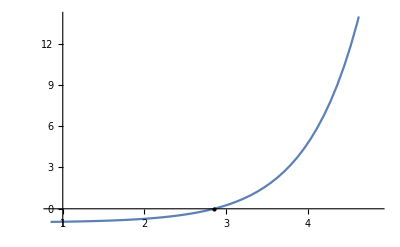

```mathematica
(* fractal dimensions of the spectrum using effective bandwidths as box widths *)
Block[{ts=1.,tw=1./10.,vpp,vpa,vppN,vpaN,bandlist,bandlistN,i=13,gam,gamN,τ0,q0=10},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+1,tw,ts]]];
Print["les spectres sont calculés !"];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=Fibonacci[i+2]^-q Plus@@((bandlist)^-τ);
gamN=Fibonacci[i+3]^-q Plus@@((bandlistN)^-τ);
(* Subscript[D, 0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->q0)-1,{τ,-1}];
Print["τ(q=",q0,")=",τ0];
(* vérif que FindRoot ne s'est pas planté *)
Print[Plot[(gamN/gam/.q->q0)-1,{τ,τ0-2,τ0+2},Epilog->{PointSize[Medium],Point[{τ0,0}]}]]
(*ListPlot[{vpp,vpa},Joined->True]*)
]
```

```mathematica
(* Compute the fractal dimension Subscript[D, q0] for a system of size fib(i+2) *)
Clear[FractalD];
FractalD[i_,tw_,ts_,q0_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN,gam,gamN,τ0},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+1,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=Fibonacci[i+2]^-q Plus@@((bandlist)^-τ);
gamN=Fibonacci[i+3]^-q Plus@@((bandlistN)^-τ);
(* Subscript[D, q0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->q0)-1,{τ,0}];
τ0
]
```

Pourquoi a-t-on D_(q>1)≃1/2 et D_(q<1)=1 quand t_w=t_s ??

```mathematica
FractalD[13,2.5,2.5,20]
```

10.

Because Γ^(n+1)/Γ^n=ω^q((Σ(Δ^(n+1)))^(-τ(q)))/((Σ(Δ^n))^(-τ(q)))=1 it is hard to compute τ(q) but easy to get q(τ).
We have
q(τ) = (B^n(τ)-B^(n+1)(τ))/(Log(q))
where
B^n(τ)=Log[(Σ(Δ^n))^-τ]

Next, we want to compute f-α. Easy!
α(τ)=(q'(τ))^-1
and
f(α(τ)) = q(τ)α(τ) - τ

Seems to converge way better is we compute Γ^(n+2)/Γ^n rather than Γ^(n+1)/Γ^n. Why?

```mathematica
(* Return banlists *)
BandLists[i_,tw_,ts_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+2 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+2,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+2,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
{bandlist,bandlistN}
]
```

```mathematica
(* Plot τ -> {α(τ),f(α(τ))} *)
Clear[FractalFa];
FractalFa[τmin_,τmax_,bandlist_,bandlistN_]:=Block[{q,alpha,f,om=N[2/(1+√5)]},
(* q(τ) *)
q=Log[Plus@@((bandlist)^-τ)/Plus@@((bandlistN)^-τ)]/Log[om^2];
(*Print[ParametricPlot[{q,τ},{τ,-10,10},AxesLabel->{"q","τ(q)"}]];*)
alpha=1./D[q,τ];
ParametricPlot[{alpha,alpha q-τ},{τ,τmin,τmax},AspectRatio->1,PlotRange->All,AxesLabel->{"α","f(α)"}]
]
```

```mathematica
{b,bnew}=BandLists[14,.1,1.];
```

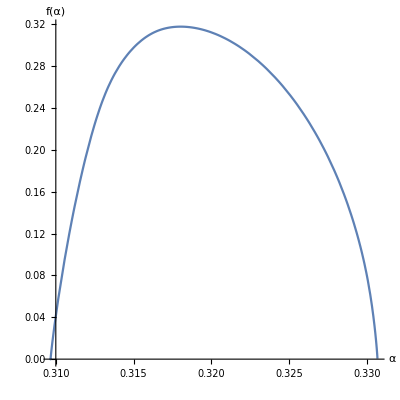

```mathematica
p=FractalFa[-100,100,b,bnew]
```

```mathematica
ClearAll[f,alpha];
exactFA[ρ_]:=Block[{z=ρ/2,barz=ρ^2,ω=N[1/GoldenRatio],f,alpha},
alpha=Log[ω]/(x Log[z]+(1-2x)/3 Log[barz]);
f=(x Log[3x/2]-(1+x)Log[(1+x)^(1/3)]+(1-2x)Log[(1-2x)^(1/3)])/(x Log[z]+(1-2x)/3 Log[barz]);
{alpha,f}
]
```

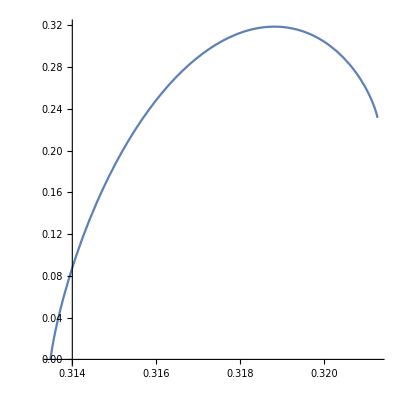

```mathematica
pth=ParametricPlot[exactFA[.1],{x,0,1/2},PlotRange->All,AspectRatio->1]
```

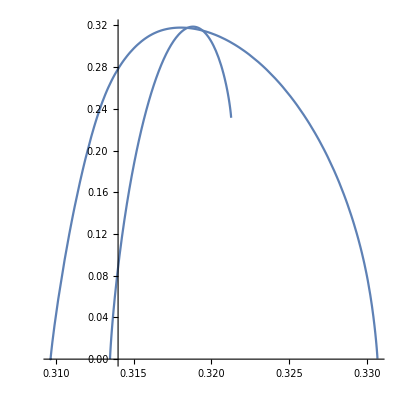

```mathematica
Show[pth,p]
```

#### Tests

```mathematica
(* asymptotically exact solution in the ρ->0 limit *)
exactFD[ρ_,q_]:=Block[{ω=1/GoldenRatio,z,barz},
z=ρ/2;
barz=ρ^2;
τ/.FindRoot[2 ω^(2q)z^-τ+ω^(3q)barz^-τ-1,{τ,10}]
]
```

```mathematica
start=2;
stop=16;
d0=ParallelTable[FractalD[i,1/10.,1.,0],{i,start,stop}]
```

Système de taille fib(n), n = 4

Système de taille fib(n), n = 6

Système de taille fib(n), n = 8

Système de taille fib(n), n = 10

Système de taille fib(n), n = 5

Système de taille fib(n), n = 7

Système de taille fib(n), n = 9

Système de taille fib(n), n = 11

Système de taille fib(n), n = 12

Système de taille fib(n), n = 13

Système de taille fib(n), n = 14

Système de taille fib(n), n = 15

Système de taille fib(n), n = 16

Système de taille fib(n), n = 17

Système de taille fib(n), n = 18

{-0.468077,-0.26209,-0.367179,-0.292778,-0.336534,-0.306884,-0.325309,-0.313124,-0.320869,-0.315809,-0.319057,-0.316947,-0.318307,-0.317426,-0.317995}

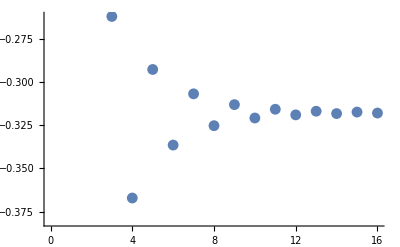

-0.314387

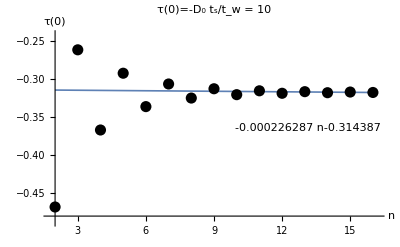

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[start,stop],d0}];
Print[ListPlot[data]];
fit=LinearModelFit[data[[start+10;;]],n,n];
Print[Normal[fit]/.n->0];
plot=Plot[Normal@fit,{n,start,stop},PlotRange->{{start-0.2,stop+0.2},{Min[d0]-0.02,Max[d0]+0.02}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"n","τ(0)"},PlotLabel->"τ(0)=-D_0 \n t_s/t_w = 10",PlotStyle->Thickness[th],PlotLegends->Placed[Normal@fit,{Right,Center}]];
Print[plot];
(*Export[dir<>"/data/hausdorff.pdf",plot];*)
]
```

```mathematica
start=2;
stop=16;
d2=ParallelTable[FractalD[i,1/2.,1.,2],{i,start,stop}]
```

Système de taille fib(n), n = 4

Système de taille fib(n), n = 6

Système de taille fib(n), n = 8

Système de taille fib(n), n = 10

Système de taille fib(n), n = 5

Système de taille fib(n), n = 7

Système de taille fib(n), n = 9

Système de taille fib(n), n = 11

Système de taille fib(n), n = 12

Système de taille fib(n), n = 13

Système de taille fib(n), n = 14

Système de taille fib(n), n = 15

Système de taille fib(n), n = 16

Système de taille fib(n), n = 17

Système de taille fib(n), n = 18

{0.72461,0.605398,0.679505,0.631598,0.664941,0.640894,0.658364,0.645304,0.654958,0.647685,0.653101,0.649019,0.652069,0.649773,0.651492}

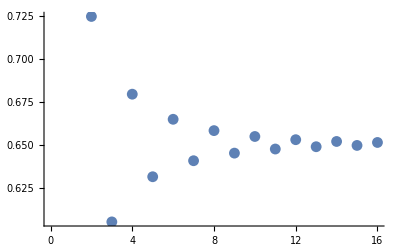

0.655441

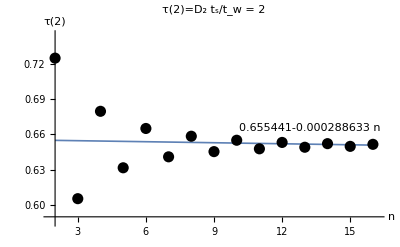

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[start,stop],d2}];
Print[ListPlot[data]];
fit=LinearModelFit[data[[start+11;;]],n,n];
Print[Normal[fit]/.n->0];
plot=Plot[Normal@fit,{n,start,stop},PlotRange->{{start-0.2,stop+0.2},{Min[d2]-0.02,Max[d2]+0.02}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"n","τ(2)"},PlotLabel->"τ(2)=D_2 \n t_s/t_w = 2",PlotStyle->Thickness[th],PlotLegends->Placed[Normal@fit,{Right,Center}]];
Print[plot];
(*Export[dir<>"/data/renyi_entropy_2.pdf",plot];*)
]
```

```mathematica
start=2;
stop=16;
d20=ParallelTable[FractalD[i,1/2.,1.,20],{i,start,stop}]
```

Système de taille fib(n), n = 4

Système de taille fib(n), n = 6

Système de taille fib(n), n = 8

Système de taille fib(n), n = 10

Système de taille fib(n), n = 5

Système de taille fib(n), n = 7

Système de taille fib(n), n = 9

Système de taille fib(n), n = 11

Système de taille fib(n), n = 12

Système de taille fib(n), n = 13

Système de taille fib(n), n = 14

Système de taille fib(n), n = 15

Système de taille fib(n), n = 16

Système de taille fib(n), n = 17

Système de taille fib(n), n = 18

{11.208,8.64141,10.3762,8.72053,10.2621,8.7331,10.2458,8.73509,10.2434,8.7354,10.2431,8.73545,10.243,8.73546,10.243}

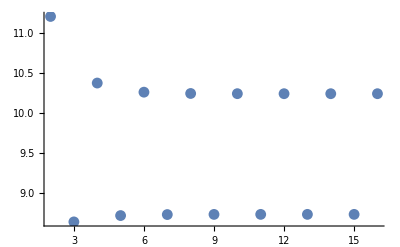

10.24728.73466

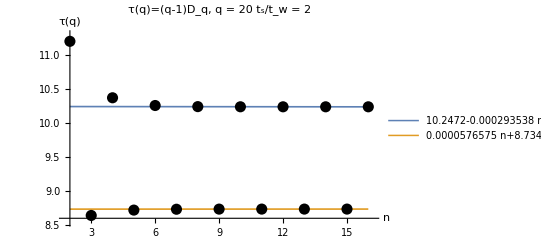

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[start,stop],d20}];
Print[ListPlot[data,PlotRange->All]];
fitSup=LinearModelFit[data[[start+5;;;;2]],n,n];
fitInf=LinearModelFit[data[[start+6;;;;2]],n,n];
Print[Normal[fitSup]/.n->0,Normal[fitInf]/.n->0];
plot=Plot[{Normal@fitSup,Normal@fitInf},{n,start,stop},PlotRange->{{start-0.2,stop+0.2},{Min[d20]-0.1,Max[d20]+0.1}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"n","τ(q)"},PlotLabel->"τ(q)=(q-1)D_q, q = 20 \n t_s/t_w = 2",PlotStyle->Thickness[th],PlotLegends->Placed[{Normal@fitSup,Normal@fitInf},{Right,Center}]];
Print[plot];
Export[dir<>"/data/renyi_q20_2.pdf",plot];
]
```

#### Comparison asymptotically exact/numerical solution in the ρ → 0 limit.

```mathematica
Col[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

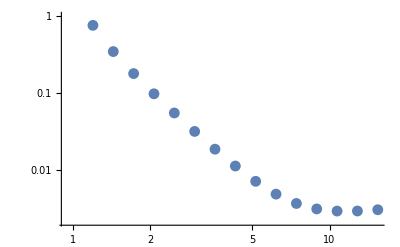

{{1.2,0.766154},{1.44,0.349178},{1.728,0.180567},{2.0736,0.0985582},{2.48832,0.0554797},{2.98598,0.031921},{3.58318,0.0187519},{4.29982,0.0113272},{5.15978,0.00716182},{6.19174,0.00487714},{7.43008,0.0036859},{8.9161,0.00312892},{10.6993,0.00293474},{12.8392,0.00294191},{15.407,0.00305458}}

```mathematica
errq0=Block[{i=11,listρ,numd2,exactd2,q=0,dat},
(* ρ = Subscript[t, w]/Subscript[t, s] *)
listρ=Table[1.2^-it,{it,1,15}];
(* numerical Rényi entropy for ρ in listρ *)
numd2=ParallelMap[FractalD[i,#,1.,q]&,listρ];
(* asymptotically exact Rényi entropy for ρ in listρ *)
exactd2=exactFD[#,q]&/@listρ;
dat=Col[listρ^-1,Abs[numd2-exactd2]/Abs[q-1]];
Print[ListLogLogPlot[dat]];
dat
]
```

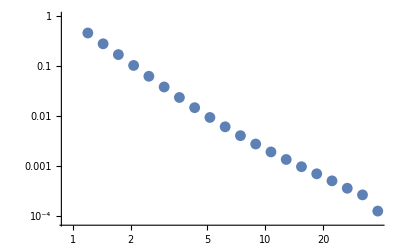

{{1.2,0.46567},{1.44,0.282547},{1.728,0.171475},{2.0736,0.103865},{2.48832,0.0629678},{2.98598,0.0383716},{3.58318,0.0236136},{4.29982,0.0147414},{5.15978,0.00937203},{6.19174,0.00608521},{7.43008,0.00404104},{8.9161,0.00274441},{10.6993,0.00190304},{12.8392,0.00134333},{15.407,0.000961199},{18.4884,0.000693302},{22.1861,0.000500225},{26.6233,0.000355357},{31.948,0.000261545},{38.3376,0.00012361}}

```mathematica
errq2=Block[{i=11,listρ,numd2,exactd2,q=2,dat},
(* ρ = Subscript[t, w]/Subscript[t, s] *)
listρ=Table[1.2^-it,{it,1,20}];
(* numerical Rényi entropy for ρ in listρ *)
numd2=ParallelMap[FractalD[i,#,1.,q]&,listρ];
(* asymptotically exact Rényi entropy for ρ in listρ *)
exactd2=exactFD[#,q]&/@listρ;
dat=Col[listρ^-1,Abs[numd2-exactd2]/Abs[q-1]];
Print[ListLogLogPlot[dat]];
dat
]
```

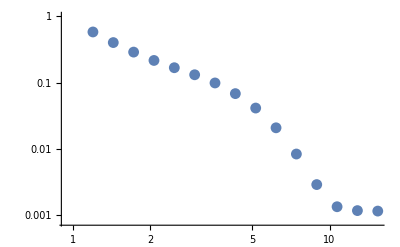

{{1.2,0.583371},{1.44,0.403642},{1.728,0.289804},{2.0736,0.216878},{2.48832,0.168454},{2.98598,0.13188},{3.58318,0.099184},{4.29982,0.0684848},{5.15978,0.0414876},{6.19174,0.020888},{7.43008,0.0083965},{8.9161,0.00290486},{10.6993,0.00134497},{12.8392,0.00117587},{15.407,0.00115637}}

```mathematica
errq10=Block[{i=11,listρ,numd2,exactd2,q=10,dat},
(* ρ = Subscript[t, w]/Subscript[t, s] *)
listρ=Table[1.2^-it,{it,1,15}];
(* numerical Rényi entropy for ρ in listρ *)
numd2=ParallelMap[FractalD[i,#,1.,q]&,listρ];
(* asymptotically exact Rényi entropy for ρ in listρ *)
exactd2=exactFD[#,q]&/@listρ;
dat=Col[listρ^-1,Abs[numd2-exactd2]/Abs[q-1]];
Print[ListLogLogPlot[dat]];
dat
]
```

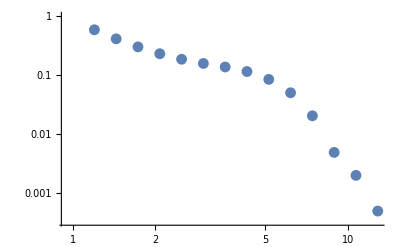

{{1.2,0.594369},{1.44,0.417058},{1.728,0.304574},{2.0736,0.232991},{2.48832,0.187852},{2.98598,0.159287},{3.58318,0.138782},{4.29982,0.116234},{5.15978,0.0854744},{6.19174,0.0506766},{7.43008,0.0206011},{8.9161,0.00492451},{10.6993,0.00200879},{12.8392,0.000497053}}

```mathematica
errq20=Block[{i=11,listρ,numd2,exactd2,q=20,dat},
(* ρ = Subscript[t, w]/Subscript[t, s] *)
listρ=Table[1.2^-it,{it,1,14}];
(* numerical Rényi entropy for ρ in listρ *)
numd2=ParallelMap[FractalD[i,#,1.,q]&,listρ];
(* asymptotically exact Rényi entropy for ρ in listρ *)
exactd2=exactFD[#,q]&/@listρ;
dat=Col[listρ^-1,Abs[numd2-exactd2]/Abs[q-1]];
Print[ListLogLogPlot[dat]];
dat
]
```

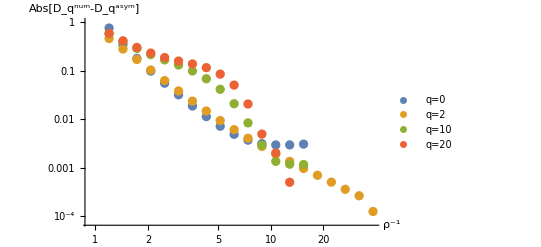

```mathematica
ListLogLogPlot[{errq0,errq2,errq10,errq20},PlotLegends->{"q="<>#&/@{"0","2","10","20"}},AxesLabel->{"ρ^-1",Abs[Subscript[D, q]^num-Subscript[D, q]^asym]}]
Export[dir<>"/data/numerical_vs_asymptotic_FD.pdf",%];
```